### This file contains problem 1

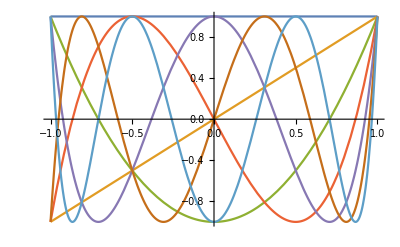

-2/3

2

```mathematica
t[x_,i_]:=Switch[i,0,1,1,x,2,2 x^2-1,3,4 x^3-3x,4,8 x^4-8 x^2+1,5,16 x^5-20 x^3+5x,6,32 x^6-48 x^4+18 x^2-1] (* Set up Polynomials *)
Plot[{t[x,0],t[x,1],t[x,2],t[x,3],t[x,4],t[x,5],t[x,6]},{x,-1,1}]
Integrate[t[x,0]t[x,2],{x,-1,1}](* Test Orthogonality, Is not orthogonal because integral with different other Chebyshev polynomial isn't zero on our domain *)
Integrate[t[x,0]t[x,0],{x,-1,1}] (* Test Normailiztion, Is not normalized because integral with self is not equal to one *)
```